## Initialization

```mathematica
<<FunctionApproximations`
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"ieee754_floating_point.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"ieee754_floating_point_evaluation.wl"}]];
```

```mathematica
SetFloatingPointFormat[binary64];
SetRoundingMode[NearestTiesToEven];
```

```mathematica
On[Assert]
```

```mathematica
?IEEE754FloatingPoint`*
```

Syntax::sntxf: "?" cannot be followed by "IEEE754FloatingPoint`*".

Extra bits for argument reduction:

```mathematica
κ3=18
```

18

Characteristics of the floating-point model:

```mathematica
M=binary64[[1]]
```

53

```mathematica
𝔲[x_]:=FromRepresentation[Representation[x]+1]-x
```

```mathematica
Assert[𝔲[1]==2^(1-M)]
```

```mathematica
γ[n_]:=n 2^-M/(1-n 2^-M)
```

## Approximation of π/2

This section verifies the error bounds for the approximations of π/2.

### Two - Term Approximation

```mathematica
κ1;κ′1;C1;δC1;
```

```mathematica
Begin["TwoTermApproximation`"]
```

TwoTermApproximation`

```mathematica
Bits[π/2]
```

0|01111111111|1001001000011111101101010100010001000010110100011000;0100011010…

```mathematica
κ1=8;
κ′1=5;
```

```mathematica
C1=Truncate[κ1,π/2];
```

```mathematica
Assert[C1==Truncate[κ′1,π/2]]
```

```mathematica
δC1=CorrectlyRound[π/2-C1];
```

```mathematica
Assert[Abs[π/2-C1-δC1]<=2^(κ′1-M-1)𝔲[π/2]]
```

The upper bound on the error of the approximation is very pessimistic:

```mathematica
N[{Abs[π/2-C1-δC1],2^(κ′1-M-1)𝔲[π/2]},20]
```

{8.478427660368899644×10^-32,3.9443045261050590271×10^-31}

That's probably because there are three zeroes after δC1:

```mathematica
Bits[π/2-C1]
```

0|01111001111|1000010001101001100010011000110011000101000101110000;0001101110…

```mathematica
Assert[Abs[δC1]<2^κ′1(1+2^(-M-1))𝔲[π/2]]
```

```mathematica
N[{Abs[δC1],2^κ′1(1+2^(-M-1))𝔲[π/2]},20]
```

{5.3903028581581189681×10^-15,7.1054273576010022531×10^-15}

```mathematica
HexLiteral[C1]
```

0x1.921FB54442D00p0

```mathematica
HexLiteral[δC1]
```

0x1.8469898CC5170p-48

```mathematica
End[]
```

TwoTermApproximation`

### Three - Term Approximation

```mathematica
κ2;κ′2;κ″2;C2;C′2;δC2;
```

```mathematica
Begin["ThreeTermApproximation`"]
```

ThreeTermApproximation`

```mathematica
Bits[π/2]
```

0|01111111111|1001001000011111101101010100010001000010110100011000;0100011010…

The paper has wrong values for κ′2 and κ″2:

```mathematica
κ2=18;
κ′2=14;
κ″2=15;
```

```mathematica
C2=Truncate[κ2,π/2];
```

```mathematica
Assert[C2==Truncate[κ′2,π/2]]
```

```mathematica
C′2=Truncate[κ2,π/2-C2];
```

```mathematica
Assert[C′2==Truncate[κ″2,π/2-C2]]
```

```mathematica
δC2=CorrectlyRound[π/2-C2-C′2];
```

```mathematica
Assert[Abs[π/2-C2-C′2-δC2]<=2^(κ′2+κ″2-2 M-1)𝔲[π/2]]
```

Here the upper bound on the error of the approximation is tight:

```mathematica
N[{Abs[π/2-C2-C′2-δC2],2^(κ′2+κ″2-2 M-1)𝔲[π/2]},20]
```

{5.2784739969746682659×10^-40,7.3468396926392969248×10^-40}

That’s because the first bit after δC2 is one:

```mathematica
Bits[π/2-C2-C′2]
```

0|01110110010|1001100010100010111000000011011100000111001101000100;1010010000…

```mathematica
Assert[Abs[δC2]<2^(κ′2+κ″2-M)(1+2^(-M-1))𝔲[π/2]]
```

```mathematica
N[{Abs[δC2],2^(κ′2+κ″2-M)(1+2^(-M-1))𝔲[π/2]},20]
```

{1.056299906698742764×10^-23,1.3234889800848443533×10^-23}

```mathematica
HexLiteral[C2]
```

0x1.921FB54440000p0

```mathematica
HexLiteral[C′2]
```

0x1.68C234C4C0000p-39

```mathematica
HexLiteral[δC2]
```

0x1.98A2E03707345p-77

```mathematica
End[]
```

ThreeTermApproximation`

## Argument Reduction

This section verifies the error bounds on argument reduction.

### Argument Reduction Using the Two-Term Approximation

```mathematica
Begin["TwoTermReduction`"]
```

TwoTermReduction`

```mathematica
xInterval=Interval[{-2^κ1 CorrectlyRound[π/2],2^κ1 CorrectlyRound[π/2]}];
```

Bound on n:

```mathematica
nIntervals=IEEEEvaluateWithAbsoluteError[xInterval CorrectlyRound[2/π]]
```

{Interval[{-256,256}],Interval[{-1/70368744177664,1/70368744177664}]}

```mathematica
nIntervalBeforeRounding=nIntervals[[1]]+nIntervals[[2]];
```

```mathematica
Assert[Max[Abs[nIntervalBeforeRounding]]<=2^κ1(1+γ[3])]
```

```mathematica
N[{Max[Abs[nIntervalBeforeRounding]],2^κ1(1+γ[3])},20]
```

{256.00000000000001421,256.00000000000008527}

```mathematica
nInterval=Round[nIntervalBeforeRounding]
```

Interval[{-256,256}]

The reason why the error bound on n is overly broad is that the rounding errors on the constants largely cancel:

```mathematica
δ1=CorrectlyRound[π/2]/(π/2)-1;
```

```mathematica
δ2=CorrectlyRound[2/π]/(2/π)-1;
```

```mathematica
N[{δ1,δ2}/𝔲[1/2],20]
```

{-0.35111610424720845605,0.55684654978214983076}

Bounds on misrounding.  Note that the second kind always has a larger error:

```mathematica
misroundingBound1=(π/4)(γ[2]/(1+γ[2]))(2^(κ1+1)-1);
```

```mathematica
N[misroundingBound1]
```

8.9115×10^-14

```mathematica
misroundingBound2=(π/4)γ[2](2^(κ1+1)+1);
```

```mathematica
N[misroundingBound2]
```

8.94638×10^-14

Bounds on δy:

```mathematica
δyInterval=IEEEEvaluateWithAbsoluteError[nInterval δC1];
```

```mathematica
Assert[Max[δyInterval[[2]]]<=Max[δyInterval[[1]]]γ[1]]
```

```mathematica
N[{Max[δyInterval[[2]]],Max[δyInterval[[1]]]γ[1]}]
```

{1.00974×10^-28,1.53202×10^-28}

Error on the approximation of π/2:

```mathematica
ζ=C1+δC1-π/2
```

124451306656115542615260972311/79228162514264337593543950336-π/2

The bound on ζ is pessimistic because C1 + δC1 is an unusually good approximation:

```mathematica
Assert[ζ<=2^(κ′1-M-1)𝔲[π/2]]
```

```mathematica
N[{ζ,2^(κ′1-M-1)𝔲[π/2]},20]
```

{-8.478427660368899644×10^-32,3.9443045261050590271×10^-31}

Error on the overall reduction.  As expected, the bound is pessimistic:

```mathematica
reductionInterval=ζ nInterval + δyInterval[[2]];
```

```mathematica
Assert[Max[reductionInterval]<2^(κ1+κ′1-M+1)𝔲[π/2]]
```

```mathematica
N[{Max[reductionInterval],2^(κ1+κ′1-M+1)𝔲[π/2]},20]
```

{1.2267897067883389418×10^-28,4.0389678347315804437×10^-28}

Threshold for dangerous rounding:

```mathematica
angleReducedThreshold = 2^(κ1+κ′1+κ3-M+2)
```

1/1048576

```mathematica
Denominator[angleReducedThreshold]//Log2
```

20

```mathematica
N[angleReducedThreshold]
```

9.53674×10^-7

```mathematica
End[]
```

TwoTermReduction`

### Argument Reduction Using the Three-Term Approximation

```mathematica
Begin["ThreeTermReduction`"]
```

ThreeTermReduction`

```mathematica
xInterval=Interval[{-2^κ2 CorrectlyRound[π/2],2^κ2 CorrectlyRound[π/2]}];
```

Bound on n:

```mathematica
nIntervals=IEEEEvaluateWithAbsoluteError[xInterval CorrectlyRound[2/π]]
```

{Interval[{-262144,262144}],Interval[{-1/68719476736,1/68719476736}]}

```mathematica
nIntervalBeforeRounding=nIntervals[[1]]+nIntervals[[2]];
```

```mathematica
Assert[Max[Abs[nIntervalBeforeRounding]]<=2^κ2(1+γ[3])]
```

```mathematica
N[{Max[Abs[nIntervalBeforeRounding]],2^κ2(1+γ[3])},20]
```

{262144.00000000001455,262144.00000000008731}

```mathematica
nInterval=Round[nIntervalBeforeRounding]
```

Interval[{-262144,262144}]

Bounds on misrounding.  Note that the second kind always has a larger error:

```mathematica
misroundingBound1=(π/4)(γ[2]/(1+γ[2]))(2^(κ2+1)-1);
```

```mathematica
N[misroundingBound1]
```

9.14322×10^-11

```mathematica
misroundingBound2=(π/4)γ[2](2^(κ2+1)+1);
```

```mathematica
N[misroundingBound2]
```

9.14326×10^-11

```mathematica
misroundingBound=Max[misroundingBound1,misroundingBound2];
```

Bounds on δy:

```mathematica
δyInterval=IEEEEvaluateWithAbsoluteError[nInterval δC2];
```

```mathematica
Assert[Max[δyInterval[[2]]]<=Max[δyInterval[[1]]]γ[1]]
```

```mathematica
N[{Max[δyInterval[[2]]],Max[δyInterval[[1]]]γ[1]}]
```

{1.92593×10^-34,3.07424×10^-34}

Error on the approximation of π/2:

```mathematica
ζ1=C2+C′2+δC2-π/2
```

1069028584064966747859680373161870783301/680564733841876926926749214863536422912-π/2

```mathematica
Assert[ζ1<=2^(κ′2+κ″2-2M-1)𝔲[π/2]]
```

```mathematica
N[{ζ1,2^(κ′2+κ″2-2M-1)𝔲[π/2]},20]
```

{5.2784739969746682659×10^-40,7.3468396926392969248×10^-40}

```mathematica
ζ2=2^(2-2M);
```

The paper should use misrounding in the following bound!

Error on the overall reduction:

```mathematica
reductionInterval=(ζ1 nInterval + δyInterval[[2]])(1+ζ2)+Interval[{-π/4-misroundingBound,π/4+misroundingBound}]ζ2;
```

```mathematica
Assert[Max[reductionInterval]<2^(κ2-2M)(2^(κ′2+κ″2+1)+3)𝔲[π/2]+2^(-2M)π]
```

```mathematica
N[{Max[reductionInterval],2^(κ2-2M)(2^(κ′2+κ″2+1)+3)𝔲[π/2]+2^(-2M)π},20]
```

{3.9054084161232440196×10^-32,3.9493491113446739675×10^-32}

Threshold for dangerous rounding:

```mathematica
angleReducedThreshold = 2^(κ3-M)(2^(κ2+κ′2+κ″2-M+2)+4)
```

65/549755813888

```mathematica
Denominator[angleReducedThreshold]//Log2
```

39

```mathematica
N[angleReducedThreshold]
```

1.18234×10^-10

```mathematica
End[]
```

ThreeTermReduction`

## Polynomials

This section derives the minimax polynomials used to approximate Sin and Cos.

### Sin

We want to compute minimax polynomials that are odd and where the term in t is linear so that the computation produces two terms, t plus a correction.  Therefore, we approximate the function sinFn below.  Note that it is singular near 0 and must therefore be replaced by its limit there.

```mathematica
Series[Sin[t],{t,0,5}]
```

t-t^3/6+t^5/120+O[t]^6

```mathematica
sinFn[t_]:=(Sin[t]-t)/t^3
```

```mathematica
Limit[sinFn[t],t->0]
```

-1/6

```mathematica
Series[sinFn[t],{t,0,2}]
```

-1/6+t^2/120+O[t]^3

#### Near Zero

Near zero the Gal and Bachelis method is not usable, so we use a plain minimax polynomial for the entire function.  We still want it to be odd and we still want to separate out the t term so we use the sinFn function with an error function suitable for the relative error.

```mathematica
Begin["SinNearZero`"]
```

SinNearZero`

```mathematica
max=1/1024;
```

```mathematica
min=-max;
```

```mathematica
argumentInterval=Interval[{min,max}]
```

Interval[{-1/1024,1/1024}]

```mathematica
sin0ApproximationResult=GeneralMiniMaxApproximation[
{t^2,If[t==0,-1/6,sinFn[t]],If[t==0,1,Sin[t]/t^3]},
{t,{0,max},1,0},
x,WorkingPrecision->30]
```

{{0,0.000753961699815828640223048022238,0.0009765625},{-0.166666666666666666666648443029+0.00833333316414932033147740536488 x,-1.82236374808329308166866751883×10^-23}}

```mathematica
sin0Approximation=Function[u, Evaluate[ u^3 (sin0ApproximationResult[[2,1]]/.x->u^2)]]
```

Function[u,u^3 (-0.166666666666666666666648443029+0.00833333316414932033147740536488 u^2)]

```mathematica
sin0ExactRelativeError = Function[u,1-(u+ sin0Approximation[u])/Sin[u]]
```

Function[u,1-(u+sin0Approximation[u])/Sin[u]]

```mathematica
sin0IEEERelativeError = Function[u,1-(u+IEEEEvaluate[ sin0Approximation[u]])/Sin[u]]
```

Function[u,1-(u+IEEEEvaluate[sin0Approximation[u]])/Sin[u]]

The plot of the relative error with floating-point evaluation is very noisy and there is no reliable way to find its extrema:

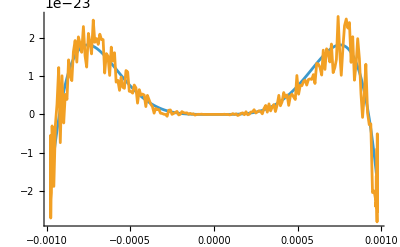

```mathematica
Plot[{sin0ExactRelativeError[x],sin0IEEERelativeError[x]},{x,min,max},WorkingPrecision->30,PlotPoints->200,PlotRange->Full]
```

Error on the minimax approximation:

```mathematica
η=sin0ApproximationResult[[2,2]]
```

-1.82236374808329308166866751883×10^-23

Error due to the floating-point evaluation:

```mathematica
sin0RoundedCoefficients=Map[CorrectlyRound,CoefficientList[sin0Approximation[x],x]]
```

{0,0,0,-6004799503160661/36028797018963968,0,2401919752500293/288230376151711744}

```mathematica
c3=sin0RoundedCoefficients[[4]];
```

```mathematica
HexLiteral[c3]
```

-0x1.5555555555555p-3

```mathematica
c5=sin0RoundedCoefficients[[6]];
```

```mathematica
HexLiteral[c5]
```

0x1.111110B40E88Ap-7

```mathematica
sin0ApproximationIntervals=IEEEEvaluateWithRelativeError[argumentInterval^3 (c3+c5 argumentInterval^2)]
```

{Interval[{-6004799503160661/38685626227668133590597632,6004799503160661/38685626227668133590597632}],Interval[{-32910091146424113535591196996633230377614699798028420881087201281/59285549689505892056868344324448208820874232148807968788202283012051522375647232,32910091146424128150607570305662412414463026960948689432960040961/59285549689505892056868344324448208820874232148807968788202283012051522375647232}]}

```mathematica
ζ=Max[Abs[sin0ApproximationIntervals[[2]]]];
```

```mathematica
N[ζ,20]
```

5.5511151231257839347×10^-16

The floating-point evaluation and rounding errors dominate the overall relative error:

```mathematica
sin0MaxRelativeError=((1+η)(1+ζ)-1)Abs[1-x/Sin[x]]/.x->max
```

8.823260559269017638856314760548547868×10^-23

```mathematica
Log2[sin0MaxRelativeError]
```

-73.2630342926785741701999839254299879653

This error preserves 20 bits after the mantissa of the result, which is sufficient for ensuring correct rounding with high probability.

```mathematica
End[]
```

Global`SinNearZero`

```mathematica
End[]
```

End::noctx: No previous context defined.

Global`